# Genetic Algorithms Code - E_g Data

## General Settings

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
(* Some unimportant error messages are switched off for future convenience *)
Off[ListInterpolation::inhr];
```

### Various Constants

```mathematica
(* Planck18 Values and other constants *)
obh2pl = 0.02237;
obh2plerr = 0.00015;
ompl = 0.3153;
omplerr = 0.0073;
σ8pl = 0.8111;
σ8err = 0.0060;
h0pl = 0.6736;
h0riess = 73.04/100;
Tcmb=2.7255;
c = 299792.458;
cH0=2997.92458;
```

## Genetic Algorithms Theory

### Genetic Algorithms Basics

```mathematica
poly[x_]:=x
polyxtox[x_]:=x^x
(* grammar={poly,Exp,Sin,Cos,Tan,Log};*)
grammar={poly,polyxtox};
(* Expression length *)
length=4;
depth=4;
rang1={-1,1};
rang2={1,Length[grammar]};
rang3={0,2};
rang4={0,9};
toursize=4;
selectionrate=0.3;
```

```mathematica
func[x_,kid_,gram_]:=Sum[kid[[i,1]] (gram[[kid[[i,2]]]]@(kid[[i,3]]x))^kid[[i,4]],{i,1,length}]
mutation[kid_]:=Module[{mut,rep},
rep={RandomInteger[{1,length}],RandomInteger[{1,depth}]};
mut=Which[rep[[2]]==1,RandomReal[rang1],rep[[2]]==2,RandomInteger[rang2],rep[[2]]==3,RandomReal[rang3],rep[[2]]==4,RandomInteger[rang4]];
ReplacePart[kid,rep->mut]]
cross[{kid1_,kid2_}]:=Module[{len},len=RandomInteger[{1,length-1}];
{Join[kid1[[1;;len]],kid2[[(len+1);;-1]]],Join[kid1[[(len+1);;-1]],kid2[[1;;len]]]}]
```

```mathematica
tournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[1,2]]
negativetournament[fit_,tours_]:=Sort[RandomSample[fit,tours],#1[[1]]>#2[[1]]&][[-1,2]]
```

```mathematica
GAevo[randomseed_,maxgens_,pop_,crossrate_,mutrate_,verbose_]:=Module[{prog,bestfitperstep,chromosomes,t1,pigs,fitness,p1,p2,maxchilds},
maxchilds=Round[selectionrate*pop,2];
SeedRandom[randomseed];
ParallelEvaluate[SeedRandom[randomseed]];
bestfitperstep={};
chromosomes=ParallelTable[{RandomReal[rang1],RandomInteger[rang2],RandomReal[rang3],RandomInteger[rang4]},{pop},{length}];
t1=AbsoluteTime[];
Do[pigs=(func[x,#,grammar]^2)&/@chromosomes;
fitness=Sort[ParallelTable[{-MemoryConstrained[TimeConstrained[chi2[pigs[[j]]],.5],10^7],j},{j,1,Length[pigs]}],#1[[1]]>#2[[1]]&];AppendTo[bestfitperstep,{fitness[[1,1]],pigs[[fitness[[1,2]]]],chromosomes[[fitness[[1,2]]]]}];p1=Partition[RandomSample[Table[negativetournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];p2=Partition[RandomSample[Table[tournament[fitness,toursize],{10maxchilds}]//Union,maxchilds],2];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<crossrate,
cross[{chromosomes[[p2[[jj,1]]]], chromosomes[[p2[[jj,2]]]]}],{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];Do[{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}=If[RandomReal[{0,1}]<mutrate,
{mutation[chromosomes[[p2[[jj,1]]]]],mutation[chromosomes[[p2[[jj,2]]]]]},{chromosomes[[p1[[jj,1]]]],chromosomes[[p1[[jj,2]]]]}];,{jj,1,Length[p1]}];
prog`int++,{maxgens}];
If[verbose==True,Print["Time taken: ",AbsoluteTime[]-t1," sec"];
Print["χ_min^2 = ",Abs[fitness[[1,1]]]];
Print["Best-fit function is: "];
Print[bestfitperstep[[-1,2]]];
bestfitperstep]];
```

## Real Data Analysis - ΛCDM Model

### Basic Functions for the wCDM Model

```mathematica
(* Note that in the dynamical data case we use directly the analytical expressions for the wCDM instead of the nCPL model that we did in the background data. This choice does not affect the overall results, since we only use them for the ΛCDM case. *)
Hwcdm[a_,w_,om_]:=√(om a^-3+(1-om)a^(-3(1+w)));
(* Growth for wCDM models *)
δ[a_,w_,Ω_]:=a Hypergeometric2F1[1/(-3w),1/2-1/(2 w),1-5/(6 w),a^(-3 w) (1-1/Ω)]
fwCDM[a_,w_,Ω_]:=aa D[Log[δ[aa,w,Ω]],aa]/.aa->a
fσ8wCDM[a_,w_,Ω_,σ8_]:=fwCDM[a,w,Ω]σ8  δ[a,w,Ω]/δ[1,w,Ω]
dAh[a_,om_,w_]:=(2a)/(√om)(Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),1-1/om]-√a Hypergeometric2F1[1/2,-1/(6w),1-1/(6w),(1-1/om)a^(-3w)]);
```

### Growth data

#### Import the E_G Compilation

```mathematica
dataEg=Import["./data/Eg_data_2022.txt","Table"];
ndatEg=Length[dataEg]
```

7

#### χ^2 of E_G

```mathematica
Σ[a_,σa_,m2_]:=2+σa (1-a)^m2-σa (1-a)^(2m2)
P2[a_,w_,Ω_,σa_,m2_]:=(Ω Σ[a,σa,m2])/fwCDM[a,w,Ω]
Eg[a_,w_,Ω_,σa_,m2_]:=P2[a,w,Ω,σa,m2]/2
chi2Eg[om_,w_,σa_,m2_]:=Sum[(1/dataEg[[i,3]](dataEg[[i,2]]-Eg[1/(1+dataEg[[i,1]]),w,om,σa,m2]))^2,{i,1,ndatEg}];
```

#### E_G Data - Maximum Likelihood Method for ΛCDM

```mathematica
minEg=FindMinimum[chi2Eg[om,-1,0,2],{om,0.3,0.31}];
ombfEg=minEg[[2,1,2]];
chifunEg=ListInterpolation[ParallelTable[chi2Eg[om,-1,0,2],{om,ombfEg-0.02,ombfEg+0.02,0.02},DistributedContexts->Automatic],{{ombfEg-0.02,ombfEg+0.02}}];
(* Params that we want to calculate the errors *)
paramsEg={om};
(* Calculation of the 1σ error according to Eq.(15.3.5) from Numerical Recipes *)
FijEg=1/2 Table[D[chifunEg[om],paramsEg[[p]],paramsEg[[d]]]/.minEg[[2]],{p,1,Length[paramsEg]},{d,1,Length[paramsEg]}];
cijEg=Inverse[FijEg];
errorsEg=Sqrt[Diagonal[cijEg]];
Print["The best fit parameter for Ω_(0  m) is: Ω_(0  m)=",ombfEg,"±",errorsEg[[1]]," with a χ^2 value: χ^2=",minEg[[1]]]
```

The best fit parameter for Ω_(0  m) is: Ω_(0  m)=0.20593±0.0287466 with a χ^2 value: χ^2=12.7605

## Genetic Algorithms

### Genetic Algorithms Calculations

#### Main Loop

```mathematica
dataP2=dataEg/.{z_,Eg_,seg_}->{1/(1+z),2 Eg,2 seg};
(* χ^2 with respect to Subscript[P, 2] *)
chi2[P2GA_]:=Sum[((dataP2[[i,2]]-(P2GA/.x->dataP2[[i,1]]))/dataP2[[i,3]])^2,{i,1,Length[dataP2]}];
```

```mathematica
generations=1500;
prog`int=0;
ProgressIndicator[Dynamic[prog`int],{0,generations}]
(*{randomseed,maxgens,population,crossoverrate,mutationrate}*)
GApop=GAevo[123456,generations,100,0.75,0.25,True];
```

Time taken: 89.043511 sec

χ_min^2 = 5.55792

Best-fit function is:

(-2.86919 x^3+4.7581 x^9-0.159751 0.180345^(0.36069 x) x^(0.36069 x))^2

#### Derived Results

```mathematica
(* Rasterize plot needs to be added here! *)
```

#### 1σ Errors

```mathematica
P2GA[x_]:=(-2.869194969500254 x^3+4.758103253931106 x^9-0.15975098755191963 0.18034521663304748^(0.36069043326609496 x) x^(0.36069043326609496 x))^2
dP2[x_,a1_,a2_,a3_]:=a1+a2 (x-1)+a3 (x-1)^2
chi2CI[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=Module[{CI},CI=Table[1/2 (Erf[1/(√2 dataP2[[i,3]])(dP2[dataP2[[i,1]],a1,a2,a3]+P2GA[dataP2[[i,1]]]-dataP2[[i,2]])]+Erf[1/(√2 dataP2[[i,3]])(dP2[dataP2[[i,1]],a1,a2,a3]-P2GA[dataP2[[i,1]]]+dataP2[[i,2]])]),{i,1,Length[dataP2]}];
Sum[(CI[[i]]-Erf[1/(√2)])^2,{i,1,Length[dataP2]}]]
chi2errtot[a1_?NumericQ,a2_?NumericQ,a3_?NumericQ]:=chi2[P2GA[x]+dP2[x,a1,a2,a3]]+chi2CI[a1,a2,a3]
```

```mathematica
fminP2err=FindMinimum[chi2errtot[a1,a2,0],{a1,0.1,0.11},{a2,0.11,0.111},MaxIterations->500]
```

{8.0727,{a1→0.0819046,a2→0.126872}}

### Comparison with ΛCDM

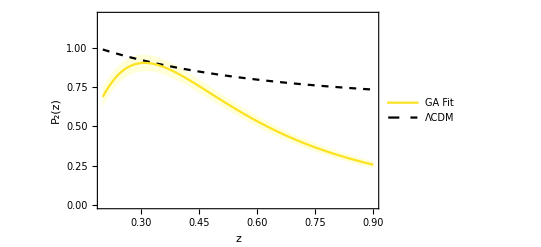

```mathematica
ϵ0={-1,0,1};
col={LightYellow,Transparent};
Egplt=Plot[{P2[1/(1+z),-1,ompl,0,2],P2GA[1/(1+z)]+dP2[1/(1+z),a1,a2,0]ϵ0/.fminP2err[[2]]}//Evaluate,{z,0.2,0.9},PlotRange->{{0.2,0.9},{0,1.2}},PlotStyle->{{Black,Dashed},col,{RGBColor["#fce222"], Bold},col},Filling->{2->{{4},col}},Frame->True,ImageSize->800,FrameLabel->{"z","P_2(z)"},FrameStyle->Black,BaseStyle->FontSize->16,PlotLegends->Placed[LineLegend[{RGBColor["#fce222"],Dashed},{"GA Fit","ΛCDM"}],Scaled[{0.8,0.8}]],Axes->None]
```

```mathematica
Export[NotebookDirectory[]<>"Egplot.pdf",Egplt,ImageResolution->1000];
```